```mathematica
l2nest = Import["/Users/mcarnright/ANN/l2.csv","CSV"]
```

{{0.492922,0.502688,0.503985,0.497994,0.494723,0.501307,0.503186,0.498964,0.49329,0.501778,0.501002,0.49989,0.490804,0.50233,0.500049,0.499972,0.496759,0.500422,0.50181,0.499263,0.491069,0.500282,0.500368,0.499953,0.493523,0.501781,0.501751,0.499692,0.481976,0.503513,19188,0.505038,0.498383,0.490667,0.500974,0.507915,0.498169,0.477144,0.503115,0.504158,0.4957,0.477326,0.50015,0.500843,0.498208,0.488108,0.503782,0.500803,0.497824,0.493681,0.501226,0.501309,0.498476,0.489153,0.502507,0.51226,0.499732,0.488604,0.502128,0.503415,0.499392}}
 |  |  |  |

```mathematica
l2= l2nest[[1]]
```

{0.492922,0.502688,0.503985,0.497994,0.494723,0.501307,0.503186,0.498964,0.49329,0.501778,0.501002,0.49989,0.490804,0.50233,0.500049,0.499972,0.496759,0.500422,0.50181,0.499263,0.491069,0.500282,0.500368,0.499953,0.493523,0.501781,0.501751,0.499692,0.481976,0.503513,19188,0.505038,0.498383,0.490667,0.500974,0.507915,0.498169,0.477144,0.503115,0.504158,0.4957,0.477326,0.50015,0.500843,0.498208,0.488108,0.503782,0.500803,0.497824,0.493681,0.501226,0.501309,0.498476,0.489153,0.502507,0.51226,0.499732,0.488604,0.502128,0.503415,0.499392}
 |  |  |  |

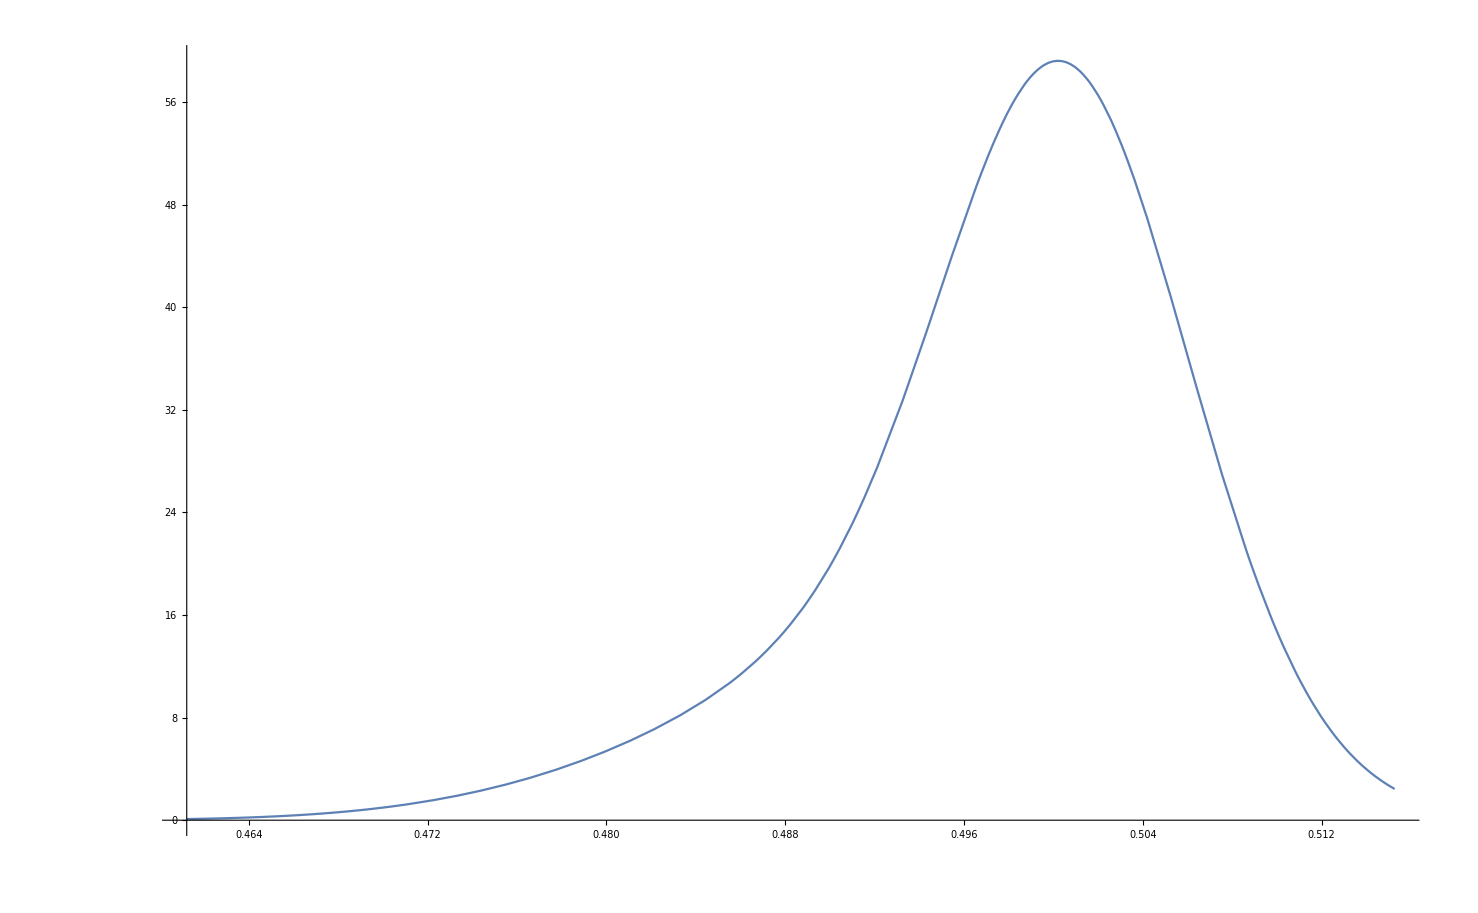

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[l2,.005],x],{x,Min[l2],Max[l2]}]
```

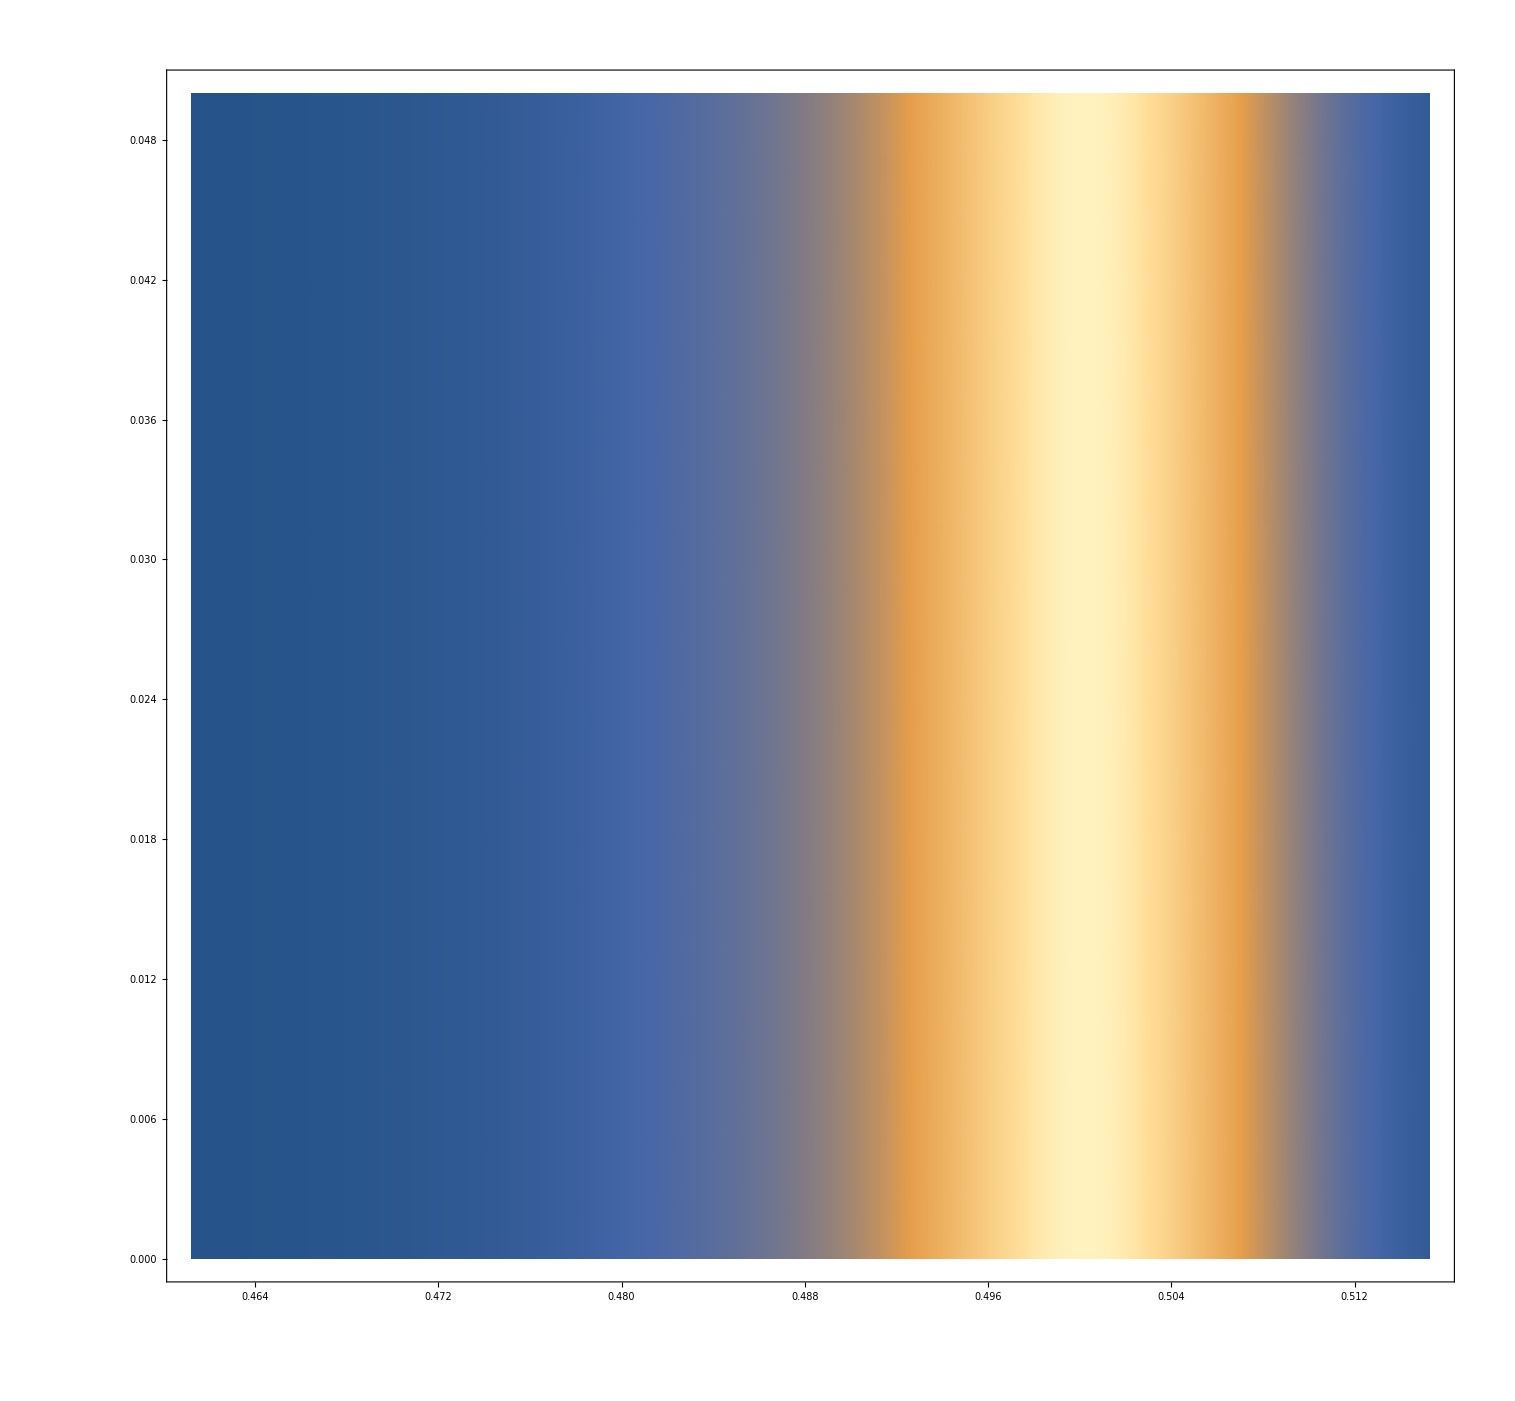

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[l2,.005],x],0}],{x,Min[l2],Max[l2]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

```mathematica
syn0nest = Import["/Users/mcarnright/ANN/syn0.csv","CSV"]


syn0= syn0nest[[1]]
```

{{1.21073,1.48791,1.1335,1.36931,1.16823,1.46489,1.04662,1.26716,1.34972,1.04945,0.995932,0.740981,0.785886,1.3822,0.60833,1.2296,0.962275,1.33487,1.11711,1.44364,1.25376,0.653202,1.22211,0.635664,1.43748,0.814412,1.39751,0.787323,1.35767,0.666489,19640,1.06008,1.25925,1.10689,1.4682,0.768625,1.15584,1.42494,1.19293,1.46609,1.22352,1.07166,0.854409,1.32237,1.03946,1.46,0.852549,1.384,0.94826,0.652129,1.01482,0.993724,1.39271,1.30979,0.611074,1.45717,0.777624,0.856669,1.36306,0.852433,1.43535}}
 |  |  |  |

{1.21073,1.48791,1.1335,1.36931,1.16823,1.46489,1.04662,1.26716,1.34972,1.04945,0.995932,0.740981,0.785886,1.3822,0.60833,1.2296,0.962275,1.33487,1.11711,1.44364,1.25376,0.653202,1.22211,0.635664,1.43748,0.814412,1.39751,0.787323,1.35767,0.666489,19640,1.06008,1.25925,1.10689,1.4682,0.768625,1.15584,1.42494,1.19293,1.46609,1.22352,1.07166,0.854409,1.32237,1.03946,1.46,0.852549,1.384,0.94826,0.652129,1.01482,0.993724,1.39271,1.30979,0.611074,1.45717,0.777624,0.856669,1.36306,0.852433,1.43535}
 |  |  |  |

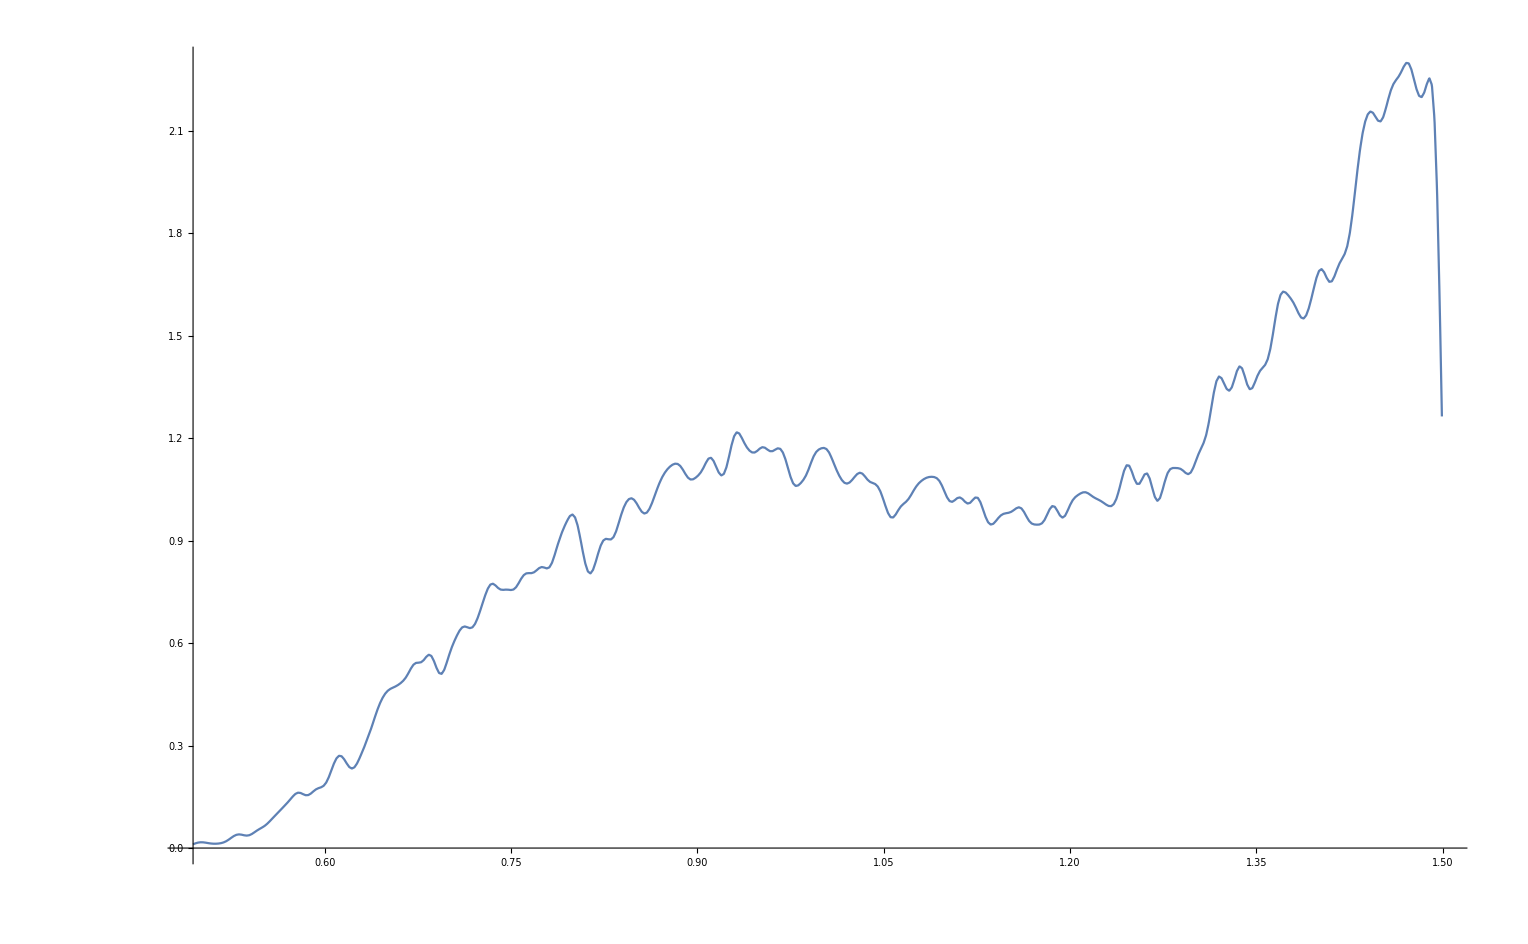

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn0,.005],x],{x,Min[syn0],Max[syn0]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn0,.005],x],0}],{x,Min[syn0],Max[syn0]},{y,0,.01},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-

```mathematica
syn1nest = Import["/Users/mcarnright/ANN/syn1.csv","CSV"]
syn1 = syn1nest[[1]]
```

{{-1.37052,1.31389,-0.951058,0.908843,0.819404,-0.873087,-0.525001,0.451423,-0.407856,0.381931,0.403169,-0.474624,0.373152,-0.424974,0.758716,-0.902974,-1.45223,1.42422,0.350809,-0.387422,0.0408933,-0.0416334,0.839608,-0.914896,-1.33799,1.2602,1.27402,-1.2976,1.20588,9904,-1.26219,-1.30457,1.24935,-1.20818,1.12039,0.59928,-0.626852,0.169917,-0.180292,1.31275,-1.44993,-0.559354,0.510928,0.532884,-0.629378,-1.48048,1.31758,-0.995763,0.959232,1.0949,-1.17832,-1.13692,1.05263,-0.983239,0.943973,0.60142,-0.669357,0.816822,-0.886962}}
 |  |  |  |

{-1.37052,1.31389,-0.951058,0.908843,0.819404,-0.873087,-0.525001,0.451423,-0.407856,0.381931,0.403169,-0.474624,0.373152,-0.424974,0.758716,-0.902974,-1.45223,1.42422,0.350809,-0.387422,0.0408933,-0.0416334,0.839608,-0.914896,-1.33799,1.2602,1.27402,-1.2976,1.20588,9904,-1.26219,-1.30457,1.24935,-1.20818,1.12039,0.59928,-0.626852,0.169917,-0.180292,1.31275,-1.44993,-0.559354,0.510928,0.532884,-0.629378,-1.48048,1.31758,-0.995763,0.959232,1.0949,-1.17832,-1.13692,1.05263,-0.983239,0.943973,0.60142,-0.669357,0.816822,-0.886962}
 |  |  |  |

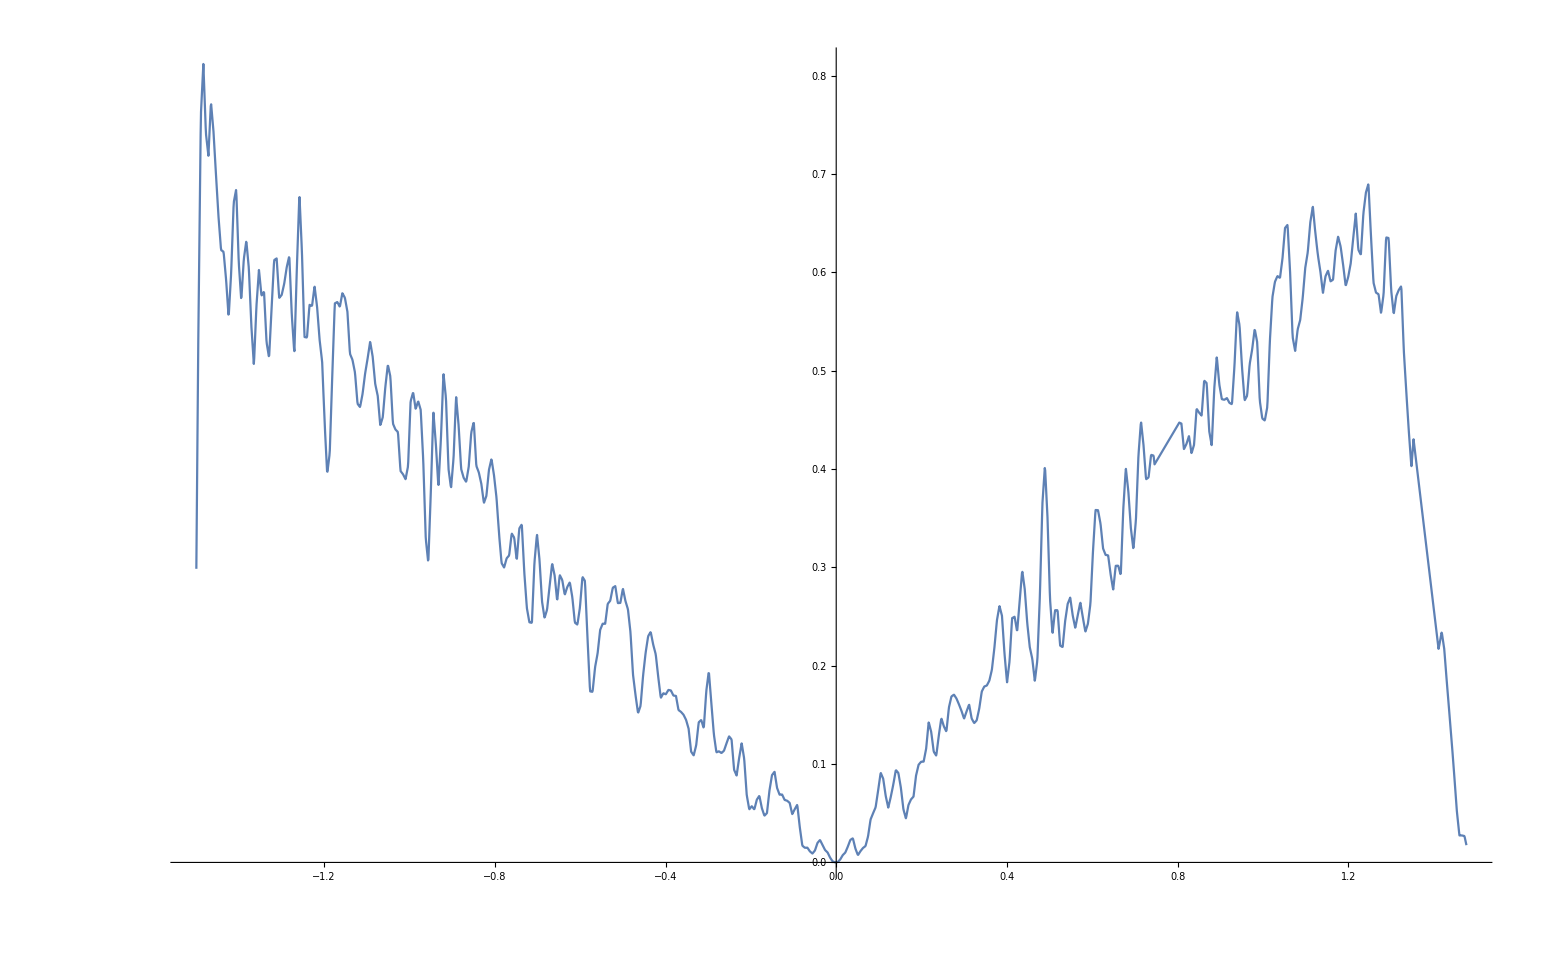

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn1,.005],x],{x,Min[syn1],Max[syn1]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn1,.005],x],0}],{x,Min[syn1],Max[syn1]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-